ARMA

AR

```mathematica
Clear[data,column1,column2,column3,matrix,variables,fi1,fi2,α,yWithCap,t,partAR,predictAR]
data = {269,321,585,871,1475,2821,3928,5943,4950,2577,523,98,184,279,409,2285,2685,3409,1824,409,151,45,68,213,546,1033,2129,2536,957,361,377,225,360,731,1638,2725,2871,2119,684,299,236,245,552,1623,3311,6721,4254,687,255,473,358,784,1594,1676,2251,1426,756,299,201,229,469,736,2042,2811,4431,2511,389,73,39,49,59,188,377,1292,4031,3495,587,105,153,387,758,1307,3465,6991,6313,3794,1836,345,382,808,1388,2713,3800,3091,2985,3790,674,81,80,108,229,399,1132,2432,3574,2935,1537,529,485,662,1000,1590,2657,3396};
```

```mathematica
column1=data⟦2;;-2⟧;
column2=data⟦;;-3⟧;
column3=ConstantArray[1,Length@data-2];
matrix={column1,column2,column3};
variables={fi1,fi2,α};
t=Length@data-2;
```

```mathematica
yWithCap=Transpose[matrix].variables;
```

```mathematica
NMinimize[1/t Sum[(data⟦i⟧-yWithCap⟦i⟧)^2,{i,3,t}],variables]
```

{0.,{fi1→-5.87522×10^-16,fi2→1.,α→-6.21704×10^-14}}

тут я не очень понимаю почему не получается верный ответ

```mathematica
partAR=LinearModelFit[Thread[{column1,column2,data⟦3;;⟧}],{fi1,fi2},{fi1,fi2}]
```

FittedModel[710.106+1.15242 fi1-0.606229 fi2]

```mathematica
{α,fi1,fi2}=partAR["BestFitParameters"]
```

{710.106,1.15242,-0.606229}

```mathematica
{fi1,fi2,α}
```

{1.15242,-0.606229,710.106}

```mathematica
predictAR=yWithCap;
```

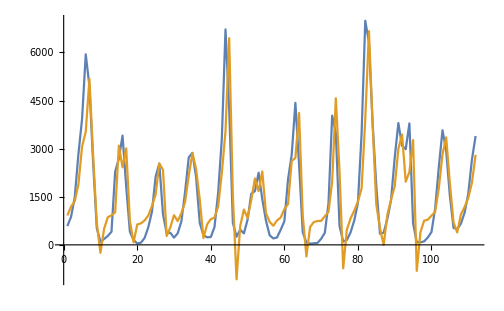

```mathematica
ListLinePlot[{data⟦3;;⟧,predictAR}]
```

MA

```mathematica
Clear[partMA,teta1,teta2,ϵ,ϵ1,ϵ2,β,predictMA]
ϵ=data⟦3;;⟧-predict;
ϵ1=ϵ⟦2;;-2⟧;
ϵ2=ϵ⟦;;-3⟧;
partMA=LinearModelFit[Thread[{ϵ1,ϵ2,ϵ⟦3;;⟧}],{teta1,teta2},{teta1,teta2}]
```

FittedModel[4.08743-0.02091 teta1-0.149523 teta2]

```mathematica
{β,teta1,teta2}=partMA["BestFitParameters"]
```

{4.08743,-0.02091,-0.149523}

```mathematica
predictMA=Transpose[{column3⟦3;;⟧,ϵ1,ϵ2}].{β,teta1,teta2};
```

```mathematica
Clear[arma]
arma=predictAR⟦3;;⟧+predictMA;
```

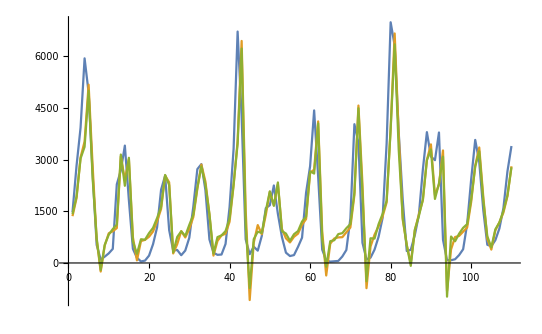

```mathematica
ListLinePlot[{data⟦5;;⟧,predictAR⟦3;;⟧,arma}]
```

Найдем прогнозное значение

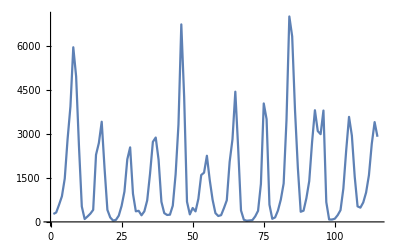

```mathematica
Clear[y,newData]
y=α+fi1*data⟦-1⟧+fi2*data⟦-2⟧+β+teta1*ϵ⟦-1⟧+teta2*ϵ⟦-2⟧;
newData=Append[data,y];
ListLinePlot[newData]
```